```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210324_disc_time_windows_and_OR_model"];
```

```mathematica
datafull=Import["../data/ccm_manipulated_396096.csv",HeaderLines->1];
```

```mathematica
(*
datavectors=datafull[[All,{9,10,11,12}]];
Length@DeleteDuplicates@datavectors
s=Table[Table[Symbol["s"<>ToString@k<>j],{j,Table[ToString@i,{i,7}]}],{k,3}]
equations=Table[Hold@s.i==0,{i,{{1,0,0,0,1,1,0},{0,1,0,1,1,1,0}}}];
AbsoluteTiming[stochioassignment=NSolve[ReleaseHold@equations,Flatten@s]];
(s/.Flatten@stochioassignment)//MatrixForm*)
(*RandomSample[DeleteDuplicates@datavectors,1]*)
```

```mathematica
stoichioforhomosapiens=Drop[Import["iAT_PLT_636_stoichiomat.csv",HeaderLines->1],None,{1}];
SparseArray@stoichioforhomosapiens
```

SparseArray[…]

```mathematica
(* stoichiometric matrix with high density *)
(* ss=Table[If[Length@DeleteCases[i,0.]≤20,Take[DeleteCases[i,0.],UpTo@20],RandomSample[DeleteCases[i,0.],20]],{i,stoichioforhomosapiens}];
SeedRandom[1];
s=Table[RandomChoice[Flatten@Join[{If[1-Total@ConstantArray[N@1/20,Length[ss[[i]]]]<10^-5,0.,1-Total@ConstantArray[N@1/20,Length[ss[[i]]]]],ConstantArray[N@1/20,Length[ss[[i]]]]}]->Flatten@{0.,ss[[i]]},20],{i,Length@ss}];
s//MatrixForm;
SparseArray@s *)
```

```mathematica
stoichiometricmatrix=stoichioforhomosapiens;
objectivefunctionamount=200;
metabolites=738;
fluxexchanges=1008;
zerosforobj=Floor[0.7*fluxexchanges,1];
steadystatevector=ConstantArray[{0,0},metabolites];
SeedRandom[6];
boundaries=RandomChoice[{0.7,0.3}->{{0,500},{0,0}},fluxexchanges];
SeedRandom[5];
(* objj=Table[Table["o["<>ToString@k<>","<>j<>"]",{j,Table[ToString@i,{i,20}]}],{k,10}]; *)
objj=Table[RandomReal[{-2,2},fluxexchanges],objectivefunctionamount];
obj=Table[ReplacePart[i,Partition[RandomSample[Range@fluxexchanges,zerosforobj],1]->0.],{i,objj}];
obj//MatrixForm;
Solutionvectors=Table[LinearProgramming[-obj[[i]],stoichiometricmatrix,steadystatevector,boundaries],{i,Length@obj}]
```

{1}
 |  |  |  |

```mathematica
Dimensions@Solutionvectors
```

{200,1008}

```mathematica
nonzerocolumnsinsolutionvectorswithstoichioforhomosapiens=Position[Table[Count[Solutionvectors[[All,i]],x_/;x≠0.],{i,fluxexchanges}],objectivefunctionamount];
```

```mathematica
AdjmatR=Transpose[stoichioforhomosapiens].stoichioforhomosapiens;
NormAdjmatR=AdjmatR/.x_/;x≠0->1;
NormAdjmatR=UpperTriangularize[NormAdjmatR,1]+LowerTriangularize[NormAdjmatR,-1];
AdjmatM=stoichioforhomosapiens.Transpose[stoichioforhomosapiens];
NormAdjmatM=AdjmatM/.x_/;x≠0->1;
NormAdjmatM=UpperTriangularize[NormAdjmatM,1]+LowerTriangularize[NormAdjmatM,-1];
```

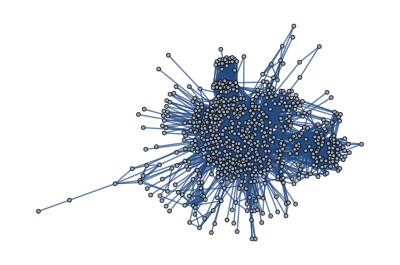

```mathematica
{AdjacencyGraph[NormAdjmatR(*,{DirectedEdges->False,VertexSize->0.3,VertexStyle->Red,VertexLabels->{1->"v1",2->"v2",3->"v3",4->"v4",5->"b1",6->"b2",7->"b3"}}*)],AdjacencyGraph[NormAdjmatM(*,{DirectedEdges->False,VertexSize->0.3,VertexStyle->Red,VertexLabels->{1->"A",2->"B",3->"C"}}*)]}
```

```mathematica
Dimensions@stoichioforhomosapiens[[All,Flatten@nonzerocolumnsinsolutionvectorswithstoichioforhomosapiens]]
```

{738,396}

```mathematica
Counts@Flatten@stoichioforhomosapiens[[All,Flatten@Position[Table[Count[Solutionvectors[[All,i]],x_/;x==0.],{i,fluxexchanges}],objectivefunctionamount]]]
```

<|0.→449225,1.→1160,-1.→1102,2.→43,-7.→6,-2.→39,3.→10,6.→2,-3.→12,8.→4,-4.→10,4.→13,-5.→8,-20.→1,14.→1,-14.→1,-9.→3,7.→5,5.→7,9.→2,-8.→1,10.→1|>

```mathematica
strial=stoichioforhomosapiens[[All,Flatten@nonzerocolumnsinsolutionvectorswithstoichioforhomosapiens]];
Dimensions@strial
```

{738,396}

```mathematica
stoichiometricmatrix=strial;
objectivefunctionamount=200;
metabolites=738;
fluxexchanges=396;
zerosforobj=Floor[0.7*fluxexchanges,1];
steadystatevector=ConstantArray[{0,0},metabolites];
SeedRandom[6];
boundaries=RandomChoice[{0.7,0.3}->{{0,500},{0,0}},fluxexchanges];
SeedRandom[5];
(* objj=Table[Table["o["<>ToString@k<>","<>j<>"]",{j,Table[ToString@i,{i,20}]}],{k,10}]; *)
objj=Table[RandomReal[{-2,2},fluxexchanges],objectivefunctionamount];
obj=Table[ReplacePart[i,Partition[RandomSample[Range@fluxexchanges,zerosforobj],1]->0.],{i,objj}];
obj//MatrixForm;
Solutionvectors=Table[LinearProgramming[-obj[[i]],stoichiometricmatrix,steadystatevector,boundaries],{i,Length@obj}]
```

{1}
 |  |  |  |

```mathematica
nonzerocolumnsinsolutionvectorswithstrial=Position[Table[Count[Solutionvectors[[All,i]],x_/;x≠0.],{i,fluxexchanges}],objectivefunctionamount];
```

```mathematica
Dimensions@nonzerocolumnsinsolutionvectorswithstrial
```

{116,1}

```mathematica
strial2=strial[[All,Flatten@nonzerocolumnsinsolutionvectorswithstrial]];
Dimensions@strial2
```

{738,116}

```mathematica
stoichiometricmatrix=strial2;
objectivefunctionamount=200;
metabolites=738;
fluxexchanges=116;
zerosforobj=Floor[0.7*fluxexchanges,1];
steadystatevector=ConstantArray[{0,0},metabolites];
SeedRandom[6];
boundaries=RandomChoice[{0.7,0.3}->{{0,500},{0,0}},fluxexchanges];
SeedRandom[5];
objj=Table[RandomReal[{-2,2},fluxexchanges],objectivefunctionamount];
obj=Table[ReplacePart[i,Partition[RandomSample[Range@fluxexchanges,zerosforobj],1]->0.],{i,objj}];
obj//MatrixForm;
Solutionvectors=Table[LinearProgramming[-obj[[i]],stoichiometricmatrix,steadystatevector,boundaries],{i,Length@obj}]
```

{1}
 |  |  |  |

```mathematica
(* with 3rd trial, solution vectors resulted as zeros *)
(* nonzerocolumnsinsolutionvectorswithstrial2=Position[Table[Count[Solutionvectors[[All,i]],x_/;x≠0.],{i,fluxexchanges}],objectivefunctionamount];
Length@nonzerocolumnsinsolutionvectorswithstrial2;
strial3=strial2[[All,Flatten@nonzerocolumnsinsolutionvectorswithstrial2]];
Dimensions@strial3
stoichiometricmatrix=strial3;
objectivefunctionamount=200;
metabolites=738;
fluxexchanges=26;
zerosforobj=Floor[0.7*fluxexchanges,1];
steadystatevector=ConstantArray[{0,0},metabolites];
SeedRandom[6];
boundaries=RandomChoice[{0.7,0.3}->{{0,500},{0,0}},fluxexchanges];
SeedRandom[5];
objj=Table[RandomReal[{-2,2},fluxexchanges],objectivefunctionamount];
obj=Table[ReplacePart[i,Partition[RandomSample[Range@fluxexchanges,zerosforobj],1]->0.],{i,objj}];
obj//MatrixForm;
Solutionvectors=Table[LinearProgramming[-obj[[i]],stoichiometricmatrix,steadystatevector,boundaries],{i,Length@obj}]; *)
```

```mathematica
nonzerocolumnsinsolutionvectorswithstrial2=Position[Table[Count[Solutionvectors[[All,i]],x_/;x≠0.],{i,fluxexchanges}],objectivefunctionamount];
nonzerocolumnsinsolutionvectorswithstrial2
```

{{22},{23},{25},{26},{39},{40},{51},{53},{54},{55},{56},{62},{63},{67},{73},{79},{81},{84},{85},{86},{87},{90},{91},{105},{108},{109}}

```mathematica
networkfeaturesdata=Solutionvectors[[All,Flatten@nonzerocolumnsinsolutionvectorswithstrial2]]*10^12;
```

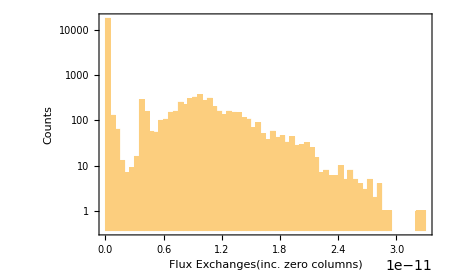
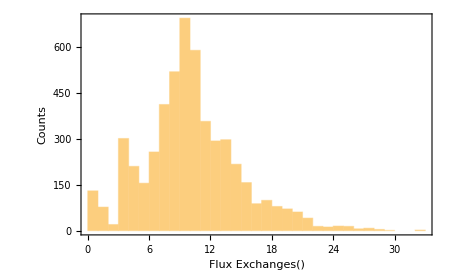

```mathematica
{Histogram[Flatten@Solutionvectors,Frame->True,ScalingFunctions->"Log",PlotRange->All,FrameLabel->{"Flux Exchanges(inc. zero columns)","Counts"},ImageSize->450],Histogram[Flatten@networkfeaturesdata,Frame->True,PlotRange->All,FrameLabel->{"Flux Exchanges()","Counts"},ImageSize->450]}
```

```mathematica
Get["../algoritm_packages/SingleNetworks-algorithm-package.wl"]
(* ?SingleNetworks`* *)
```

```mathematica
data=networkfeaturesdata;
Dimensions@data
```

{200,26}

```mathematica
snetworkgraphsinglenodes[data[[]]]
```

```mathematica
(* snetworkgraphsinglenodes[aim_,campaign_,vertexsize_,vertexlabelsize_,imagesize_,vertexcolor_] *)
```